# Alex Brinson Plotting and Animating Solutions for Fields in a Right - Triangular Hollow Waveguide

```mathematica
SetDirectory["C:\\Users\\Alex Brinson\\Documents\\Ph106c\\Animations\\TriangularWaveguideModes"] ;
```

```mathematica
(*some relevant equations*)
Hperp=1/(Keu^2-k^2)(I k Grad[H0z,{x,y}]+I Keu/Zeu Cross[zHat, Grad[E0z,{x,y}]]);  (*eq 9.261*)
Eperp=1/(Keu^2-k^2)(I k Grad[E0z,{x,y}]-I Keu *Zeu Cross[zHat, Grad[H0z,{x,y}]]);  (*eq 9.262*)
(* Laplacian[E0z,{x,y}]+(Keu^2-k^2)E0z = 0 ; Laplacian[H0z,{x,y}]+(Keu^2-k^2)H0z = 0 (*eq 9.266*)*)
(* (∇_⊥)^2 Subscript[E, 0,z]+ (Subscript[k, ϵμ]^2- k^2)Subscript[E, 0,z] = 0 ; (∇_⊥)^2 Subscript[H, 0,z]+(Subscript[k, ϵμ]^2- k^2)Subscript[H, 0,z] = 0 (*9.266*)*)

(*TE: Hperp = 1/Zeu k/Keu Cross[zHat, E0perp,{x,y}]] ; TM: Hperp = 1/Zeu Keu/k Cross[zHat, E0perp] (*eq 9.267*)*)

(*Boundary Conditions: n̂·H⃗ = 0; t̂·E⃗ = 0 ;   Subscript[E, 0,z]|_C = 0 (*9.268*)  ;   n̂·OverVector[∇]_⊥Subscript[H, 0,z]|_C = 0  (*9.269*)*)
```

```mathematica
(E⃗)_(⊥,(m,n))^TM=(i Subscript[k, m,n]^TM(ω))/Subscript[γ, m,n]^2 OverVector[∇]_⊥Subscript[E⃗, 0, Z,(m,n)]^TM = (ⅈ a)/(π (m^2+n^2))ω/c √(1-((m^2+n^2) π^2)/a^2 c^2/ω^2) { [m Cos((m π x)/a) Sin((n π y)/a) -n Cos((n π x)/a) Sin((m π y)/a)] x̂ + [m Cos((m π y)/a) Sin((n π x)/a)-n Cos((n π y)/a) Sin((m π x)/a) ]  ŷ }
(H⃗)_(⊥,(m,n))^TM=i/Subscript[γ, m,n]^2 Subscript[k, ϵ,μ]/Subscript[Z, ϵ,μ] ẑ × OverVector[∇]_⊥Subscript[E⃗, 0, Z,(m,n)]^TM =(ⅈ a Subscript[ϵ, 0] ω)/(π (m^2+n^2)){ [m Cos((m π y)/a) Sin((n π x)/a) -n Cos((n π y)/a) Sin((m π x)/a)] x̂ + [m Cos((m π x)/a) Sin((n π y)/a)-n Cos((n π x)/a) Sin((m π y)/a) ]  ŷ }
```

```mathematica
assumptions = a∈Reals&&x∈Reals&&m∈Integers&&n∈Integers&&m≥ 0&&n≥ 0&&ω∈Reals&&ϵ∈Reals&&μ∈Reals&&ϵ0∈Reals&&μ0∈Reals&&ϵ0 μ0 == 1/c^2&&√(ϵ0 μ0)==1/c&&c∈Reals;
```

```mathematica
Subscript[ψ, 4,3]^TM(x,y)=Sin[(m π x)/a] Sin[(n π y)/a]-Sin[(n π x)/a] Sin[(m π y)/a]
```

```mathematica
TM[a_,m_,n_,x_,y_]:=Sin[(m π x)/a] Sin[(n π y)/a]-Sin[(n π x)/a] Sin[(m π y)/a]
TE[a_,m_,n_,x_,y_]:=Cos[(m π x)/a] Cos[(n π y)/a]+Cos[(n π x)/a] Cos[(m π y)/a]
```

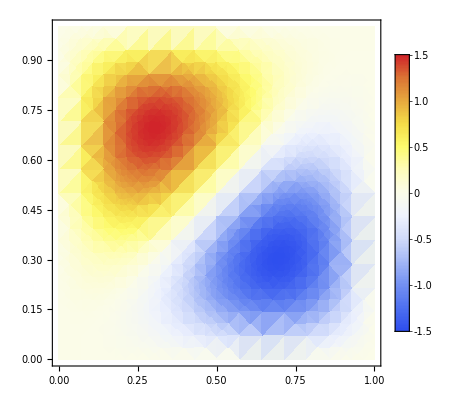

```mathematica
DensityPlot[TM[1,2,1,x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic] 
(*This is Subscript[ψ, (▲,)2,1]^TM plotted on the entire square, but our solutions only apply to the bottom/right half.*)
```

```mathematica
guideReg=Triangle[{{0,0},{1,0},{1,1}}]; (*Defines the cavity region for our right-triangular hollow waveguide.*)
```

```mathematica
Plot3D[TM[1,5,2,x,y],{x,y}∈guideReg,ColorFunction->"TemperatureMap",PlotPoints->50,PlotLabel->"ψ_(4, 3)^TM(x,y)",PlotTheme->"Scientific"]
```

-Graphics3D-

4.55454×10^-8

1.5396

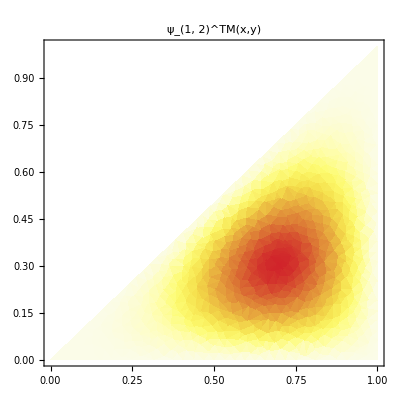

```mathematica
(*You can probably ignore this cell. I was just being stubborn and wanted the zero point on my colorbar to correspond with white*)
minVal =FindMinimum[{TM[1,1,2,x,y],{x,y}∈guideReg},{{x,.1},{y,.1}}][[1]]
maxVal=FindMaximum[{TM[1,1,2,x,y],{x,y}∈guideReg},{{x,.1},{y,.1}}][[1]]
DensityPlot[(TM[1,1,2,x,y]-minVal)/(2 Abs[maxVal-minVal])+.5,{x,y}∈guideReg,ColorFunction->"TemperatureMap",ColorFunctionScaling->False,PlotPoints->30,PlotLabel->"ψ_(1, 2)^TM(x,y)"]
```

-1.5396

-4.55454×10^-8

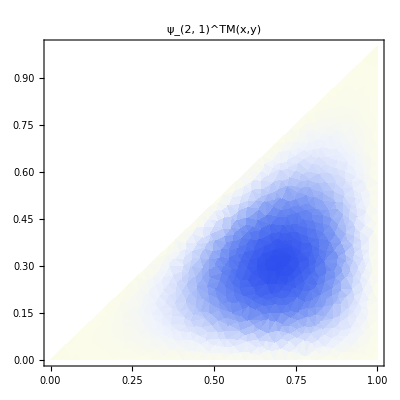

```mathematica
(*You can also ignore this cell. Same deal as before; I just wanted to show that Subscript[ψ, 2,1]^TM = -Subscript[ψ, 1,2]^TM are both really the same solution.*)
minVal =FindMinimum[{TM[1,2,1,x,y],{x,y}∈guideReg},{{x,.1},{y,.1}}][[1]]
maxVal=FindMaximum[{TM[1,2,1,x,y],{x,y}∈guideReg},{{x,.1},{y,.1}}][[1]]
DensityPlot[(TM[1,2,1,x,y]-minVal)/(2 Abs[maxVal-minVal]),{x,y}∈guideReg,ColorFunction->"TemperatureMap",ColorFunctionScaling->False,PlotPoints->30,PlotLabel->"ψ_(2, 1)^TM(x,y)"]
```

-1.59744

1.30665

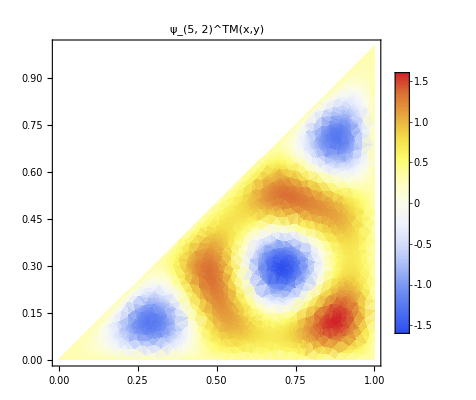

```mathematica
min52 =FindMinimum[{TM[1,5,2,x,y],{x,y}∈guideReg},{{x,.1},{y,.1}}][[1]]
max52=FindMaximum[{TM[1,5,2,x,y],{x,y}∈guideReg},{{x,.9},{y,.1}}][[1]]
DensityPlot[TM[1,5,2,x,y]*HeavisideTheta[x-y],{x,y}∈guideReg,ColorFunction->"TemperatureMap",PlotPoints->30,PlotLegends->BarLegend[{"TemperatureMap",{min52,-min52}}],PlotLabel->"ψ_(5, 2)^TM(x,y)"]
```

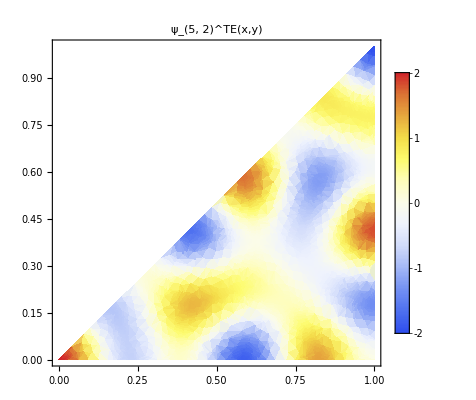

```mathematica
(*And for completeness (hehe), here's a TE solution*)
DensityPlot[(TE[1,5,2,x,y]),{x,y}∈guideReg,ColorFunction->"TemperatureMap",PlotPoints->30,PlotLabel->"ψ_(5, 2)^TE(x,y)",PlotLegends->Automatic]
```

```mathematica
(*Defining functions to Compute the perpendicular components of the solutions *)
WcutTM[m_,n_,ϵ_,μ_,a_]:=1/(√(ϵ μ))π/a √(m^2+ n^2);
KTM[m_,n_,ω_,ϵ_,μ_,a_]:=ω*√(ϵ μ)*√(1-(WcutTM[m,n,ϵ,μ,a]/ω)^2);
EperpTM[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=1/(π^2/(a)^2(m^2+n^2))(*I*) KTM[m,n,ω,ϵ,μ,a] Grad[TM[a,m,n,x,y],{x,y}];
EperpTM3D[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=1/(π^2/(a)^2(m^2+n^2))I KTM[m,n,ω,ϵ,μ,a]*Append[ Grad[TM[a,m,n,x,y],{x,y}],0];
HperpTM[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=1/(π^2/(a)^2(m^2+n^2))(*I*) ω ϵ  Cross[{0,0,1}, Append[Grad[TM[a,m,n,x,y],{x,y}],0]][[1;;2]]
HperpTM3D[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=1/(π^2/(a)^2(m^2+n^2))I ω ϵ  Cross[{0,0,1}, Append[Grad[TM[a,m,n,x,y],{x,y}],0]]
```

```mathematica
FullSimplify[I EperpTM[m,n,x,y,ω,a,"ϵ_0","μ_0"]]
FullSimplify[I HperpTM[m,n,x,y,ω,"a","ϵ_0","μ_0"]]
```

{(ⅈ √(ϵ_0 μ_0) a √(1-((m^2+n^2) π^2)/(ϵ_0 μ_0 a^2 ω^2)) ω (-n Cos[(n π x)/a] Sin[(m π y)/a]+m Cos[(m π x)/a] Sin[(n π y)/a]))/((m^2+n^2) π),-(ⅈ √(ϵ_0 μ_0) a √(1-((m^2+n^2) π^2)/(ϵ_0 μ_0 a^2 ω^2)) ω (-n Cos[(n π y)/a] Sin[(m π x)/a]+m Cos[(m π y)/a] Sin[(n π x)/a]))/((m^2+n^2) π)}

{(ⅈ a ϵ_0 ω (-n Cos[(n π y)/a] Sin[(m π x)/a]+m Cos[(m π y)/a] Sin[(n π x)/a]))/((m^2+n^2) π),(ⅈ a ϵ_0 ω (-n Cos[(n π x)/a] Sin[(m π y)/a]+m Cos[(m π x)/a] Sin[(n π y)/a]))/((m^2+n^2) π)}

```mathematica
FullSimplify[EperpTM[5,2,x,y,20,1,1,1]]
```

{(√(400-29 π^2) (5 Cos[5 π x] Sin[2 π y]-2 Cos[2 π x] Sin[5 π y]))/(29 π),(√(400-29 π^2) (-5 Cos[5 π y] Sin[2 π x]+2 Cos[2 π y] Sin[5 π x]))/(29 π)}

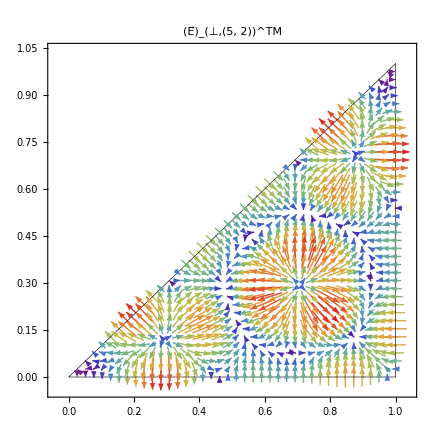

```mathematica
Show[VectorPlot[{(√(400-29 π^2) (5 Cos[5 π x] Sin[2 π y]-2 Cos[2 π x] Sin[5 π y]))/(29 π),(√(400-29 π^2) (-5 Cos[5 π y] Sin[2 π x]+2 Cos[2 π y] Sin[5 π x]))/(29 π)},{x,y}∈guideReg,VectorPoints->{40,40},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(E⃗)_(⊥,(5, 2))^TM"],Graphics[{Thickness[.001],Line[{{0,0},{1,0},{1,1},{0,0}}]}]]
```

```mathematica
FullSimplify[HperpTM[5,2,x,y,20,1,1,1]]
```

{(20 (5 Cos[5 π y] Sin[2 π x]-2 Cos[2 π y] Sin[5 π x]))/(29 π),(20 (5 Cos[5 π x] Sin[2 π y]-2 Cos[2 π x] Sin[5 π y]))/(29 π)}

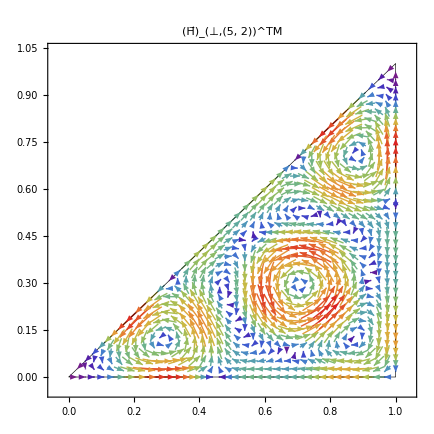

```mathematica
Show[VectorPlot[{(20 (5 Cos[5 π y] Sin[2 π x]-2 Cos[2 π y] Sin[5 π x]))/(29 π),(20 (5 Cos[5 π x] Sin[2 π y]-2 Cos[2 π x] Sin[5 π y]))/(29 π)},{x,y}∈guideReg,VectorPoints->{40,40},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(H⃗)_(⊥,(5, 2))^TM"],Graphics[{Thickness[.001],Line[{{0,0},{1,0},{1,1},{0,0}}]}]]
```

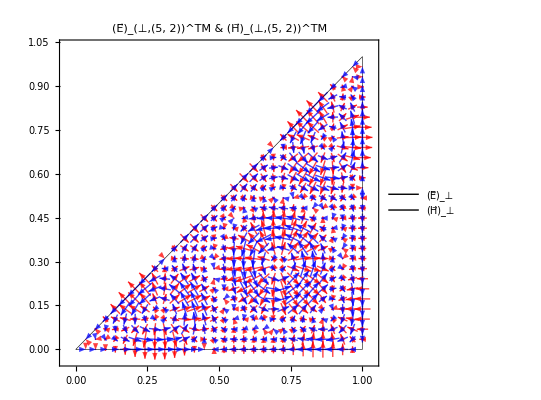

```mathematica
ePerpPlotTM=VectorPlot[{(√(400-29 π^2) (5 Cos[5 π x] Sin[2 π y]-2 Cos[2 π x] Sin[5 π y]))/(29 π),(√(400-29 π^2) (-5 Cos[5 π y] Sin[2 π x]+2 Cos[2 π y] Sin[5 π x]))/(29 π)},{x,y}∈guideReg,VectorPoints->{30,30},VectorStyle->{Red,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(E⃗)_⊥",Red}];
bPerpPlotTM=VectorPlot[{(20 (5 Cos[5 π y] Sin[2 π x]-2 Cos[2 π y] Sin[5 π x]))/(29 π),(20 (5 Cos[5 π x] Sin[2 π y]-2 Cos[2 π x] Sin[5 π y]))/(29 π)},{x,y}∈guideReg,VectorPoints->{30,30},VectorStyle->{Blue,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(H⃗)_⊥",Blue}];
Show[ePerpPlotTM,bPerpPlotTM,Graphics[{Thickness[.001],Line[{{0,0},{1,0},{1,1},{0,0}}]}],PlotLabel->"(E⃗)_(⊥,(5, 2))^TM & (H⃗)_(⊥,(5, 2))^TM"]
```

```mathematica
ETMtot[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=EperpTM3D[m,n,x,y,ω,a,ϵ,μ]+{0,0,TM[a,m,n,x,y]}
ETMtotProp[m_,n_,x_,y_,ω_,a_,ϵ_,μ_,z_,t_]:=EperpTM3D[m,n,x,y,ω,a,ϵ,μ]*(I Sin[KTM[m,n,ω,ϵ,μ,a]z-ω t])+{0,0,TM[a,m,n,x,y]}*Cos[KTM[m,n,ω,ϵ,μ,a]z-ω t]
```

```mathematica
Assuming[assumptions,FullSimplify[ETMtot[m,n,x,y,ω,a,ϵ0,μ0]]]
```

{(ⅈ a √(ϵ0 μ0-((m^2+n^2) π^2)/(a^2 ω^2)) ω (-n Cos[(n π x)/a] Sin[(m π y)/a]+m Cos[(m π x)/a] Sin[(n π y)/a]))/((m^2+n^2) π),-(ⅈ a √(ϵ0 μ0-((m^2+n^2) π^2)/(a^2 ω^2)) ω (-n Cos[(n π y)/a] Sin[(m π x)/a]+m Cos[(m π y)/a] Sin[(n π x)/a]))/((m^2+n^2) π),-Sin[(n π x)/a] Sin[(m π y)/a]+Sin[(m π x)/a] Sin[(n π y)/a]}

```mathematica
ETMtotProp[3,2,x,y,20,1,1,1,z,t]
```

{(20 √(1-(13 π^2)/400) (3 π Cos[3 π x] Sin[2 π y]-2 π Cos[2 π x] Sin[3 π y]) Sin[20 t-20 √(1-(13 π^2)/400) z])/(13 π^2),(20 √(1-(13 π^2)/400) (-3 π Cos[3 π y] Sin[2 π x]+2 π Cos[2 π y] Sin[3 π x]) Sin[20 t-20 √(1-(13 π^2)/400) z])/(13 π^2),Cos[20 t-20 √(1-(13 π^2)/400) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])}

```mathematica
Assuming[assumptions,FullSimplify[ETMtotProp[3,2,x,y,14,1,1,1,z,t]]]
```

{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])}

```mathematica
(*First, I used Manipulate[] to test plot settings/get an idea of what the animations looked like*)
Manipulate[Image[SliceVectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},ImplicitRegion[y≤x&&z==0,{x,y,z}],{x,0,1},{y,0,1},{z,-.1,.1},VectorPoints->{40,40,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.003],VectorScale->.04,BoxRatios->{1, 1, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{0, -1.4,.7},PlotLabel->"(E⃗)_(3, 2)^TM , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
(*Once I found something I liked with Manipulate, I'd construct a table of frames for the animation, and then export it as a .gif*)
crossSectionFrames=Table[Image[SliceVectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},ImplicitRegion[y≤x&&z==0,{x,y,z}],{x,0,1},{y,0,1},{z,-.1,.1},VectorPoints->{40,40,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.003],VectorScale->.04,BoxRatios->{1, 1, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{0, -1.4,.7},PlotLabel->"(E⃗)_(3, 2)^TM , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
Export["TriangleCrossSection_E_TM_3_2.gif",crossSectionFrames[[1;;Length[crossSectionFrames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[crossSectionFrames]-1)]
```

TriangleCrossSection_E_TM_3_2.gif

```mathematica
Manipulate[Image[VectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},{x,0,1},{y,0,1},{z,0,(4π)/8.23},RegionFunction-> (({#1,#2}∈guideReg)&),VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,VectorPoints->{18,18,10},BoxRatios->{1, 1,(4π)/8.3},Axes->False,ViewPoint->{-2.5,-2.75,.75},PlotLabel->"(E⃗)_(3, 2)^TM Propagating Through Right-Triangular Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
wavGuideFrames=Table[Image[VectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},{x,0,1},{y,0,1},{z,0,(4π)/8.23},RegionFunction-> (({#1,#2}∈guideReg)&),VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,VectorPoints->{18,18,10},BoxRatios->{1, 1,(4π)/8.3},Axes->False,ViewPoint->{-2.5,-2.75,.75},PlotLabel->"(E⃗)_(3, 2)^TM Propagating Through Right-Triangular Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
Export["TriangleAnimation_E_TM_3_2.gif",wavGuideFrames[[1;;Length[wavGuideFrames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[wavGuideFrames]-1)]
```

TriangleAnimation_E_TM_3_2.gif

```mathematica
Manipulate[Image[Show[SliceVectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},y==0,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,1,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{-4,-3,.75},PlotLabel->"(E⃗)_(3, 2)^TM , Surface Of Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],SliceVectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},y==x,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,30,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02]],
Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,0,0},{1,0,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=0",{.5,0,-.1}]}],Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,1,0},{1,1,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=x",{.6,.6,-.1}]}],
Graphics3D[{Thickness[.001],Line[{{1,0,0},{1,1,0},{1,1,(4π)/8.23},{1,0,(4π)/8.23},{1,0,0}}]}]],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
triangleSurfaceETM32 = Table[Image[Show[SliceVectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},y==0,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,1,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{-4,-3,.75},PlotLabel->"(E⃗)_(3, 2)^TM , Surface Of Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],SliceVectorPlot3D[{(√(196-13 π^2) (3 Cos[3 π x] Sin[2 π y]-2 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(√(196-13 π^2) (-3 Cos[3 π y] Sin[2 π x]+2 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),Cos[14 t-√(196-13 π^2) z] (Sin[3 π x] Sin[2 π y]-Sin[2 π x] Sin[3 π y])},y==x,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,30,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02]],
Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,0,0},{1,0,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=0",{.5,0,-.1}]}],Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,1,0},{1,1,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=x",{.6,.6,-.1}]}],
Graphics3D[{Thickness[.001],Line[{{1,0,0},{1,1,0},{1,1,(4π)/8.23},{1,0,(4π)/8.23},{1,0,0}}]}]],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
Export["TriangleSurface_E_TM_3_2.gif",triangleSurfaceETM32[[1;;Length[triangleSurfaceETM32]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[triangleSurfaceETM32]-1)]
```

TriangleSurface_E_TM_3_2.gif

```mathematica
(*Everything below works the same way as what's above, but applies to the transverse electric (TE) solutions*)
```

```mathematica
WcutTE[m_,n_,ϵ_,μ_,a_]:=1/(√(ϵ μ))π/a √(m^2+ n^2);
KTE[m_,n_,ω_,ϵ_,μ_,a_]:=ω*√(ϵ μ)*√(1-(WcutTE[m,n,ϵ,μ,a]/ω)^2);
EperpTE[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=-I/(π^2/(a)^2(m^2+n^2))(*I*) ω μ  Cross[{0,0,1}, Append[Grad[TE[a,m,n,x,y],{x,y}],0]][[1;;2]];
EperpTE3D[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=-1/(π^2/(a)^2(m^2+n^2))I ω μ  Cross[{0,0,1}, Append[Grad[TE[a,m,n,x,y],{x,y}],0]]
HperpTE[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=I/(π^2/(a)^2(m^2+n^2))(*I*) KTE[m,n,ω,ϵ,μ,a] Grad[TE[a,m,n,x,y],{x,y}];
HperpTE3D[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=1/(π^2/(a)^2(m^2+n^2))I KTE[m,n,ω,ϵ,μ,a]*Append[ Grad[TE[a,m,n,x,y],{x,y}],0];
```

```mathematica
FullSimplify[EperpTE[m,n,x,y,ω,"a","ϵ_0","μ_0"]]
```

{-(ⅈ a μ_0 ω (m Cos[(n π x)/a] Sin[(m π y)/a]+n Cos[(m π x)/a] Sin[(n π y)/a]))/((m^2+n^2) π),(ⅈ a μ_0 ω (m Cos[(n π y)/a] Sin[(m π x)/a]+n Cos[(m π y)/a] Sin[(n π x)/a]))/((m^2+n^2) π)}

```mathematica
FullSimplify[HperpTE[m,n,x,y,ω,"a","ϵ_0","μ_0"]]
```

{-(ⅈ a √(ϵ_0 μ_0) √(1-((m^2+n^2) π^2)/(a^2 ϵ_0 μ_0 ω^2)) ω (m Cos[(n π y)/a] Sin[(m π x)/a]+n Cos[(m π y)/a] Sin[(n π x)/a]))/((m^2+n^2) π),-(ⅈ a √(ϵ_0 μ_0) √(1-((m^2+n^2) π^2)/(a^2 ϵ_0 μ_0 ω^2)) ω (m Cos[(n π x)/a] Sin[(m π y)/a]+n Cos[(m π x)/a] Sin[(n π y)/a]))/((m^2+n^2) π)}

```mathematica
FullSimplify[EperpTE[5,2,x,y,20,1,1,1]]
```

{-(20 (2 Cos[5 π x] Sin[2 π y]+5 Cos[2 π x] Sin[5 π y]))/(29 π),(20 (2 Cos[5 π y] Sin[2 π x]+5 Cos[2 π y] Sin[5 π x]))/(29 π)}

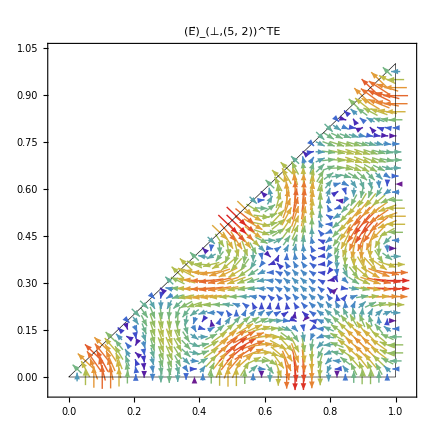

```mathematica
Show[VectorPlot[{-(20 (2 Cos[5 π x] Sin[2 π y]+5 Cos[2 π x] Sin[5 π y]))/(29 π),(20 (2 Cos[5 π y] Sin[2 π x]+5 Cos[2 π y] Sin[5 π x]))/(29 π)},{x,y}∈guideReg,VectorPoints->{40,40},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(E⃗)_(⊥,(5, 2))^TE"],Graphics[{Thickness[.001],Line[{{0,0},{1,0},{1,1},{0,0}}]}]]
```

```mathematica
FullSimplify[HperpTE[5,2,x,y,20,1,1,1]]
```

{-(√(400-29 π^2) (2 Cos[5 π y] Sin[2 π x]+5 Cos[2 π y] Sin[5 π x]))/(29 π),-(√(400-29 π^2) (2 Cos[5 π x] Sin[2 π y]+5 Cos[2 π x] Sin[5 π y]))/(29 π)}

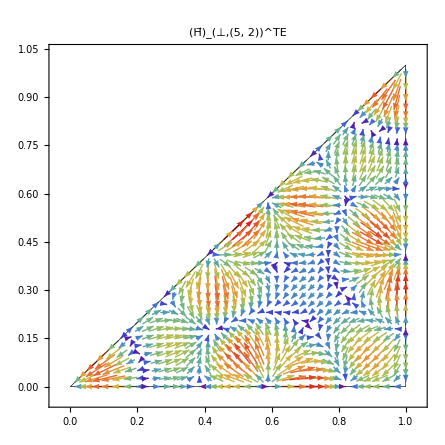

```mathematica
Show[VectorPlot[{-(√(400-29 π^2) (2 Cos[5 π y] Sin[2 π x]+5 Cos[2 π y] Sin[5 π x]))/(29 π),-(√(400-29 π^2) (2 Cos[5 π x] Sin[2 π y]+5 Cos[2 π x] Sin[5 π y]))/(29 π)},{x,y}∈guideReg,VectorPoints->{40,40},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(H⃗)_(⊥,(5, 2))^TE"],Graphics[{Thickness[.001],Line[{{0,0},{1,0},{1,1},{0,0}}]}]]
```

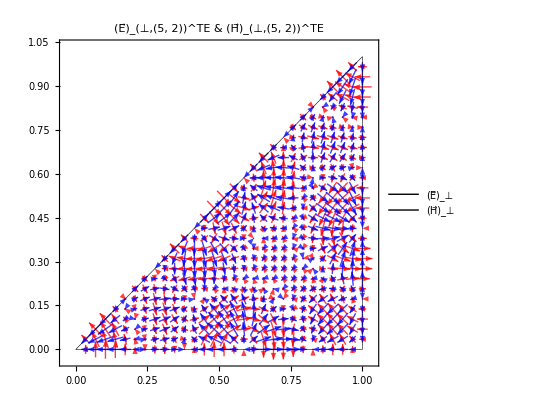

```mathematica
ePerpPlotTM=VectorPlot[{-(20 (2 Cos[5 π x] Sin[2 π y]+5 Cos[2 π x] Sin[5 π y]))/(29 π),(20 (2 Cos[5 π y] Sin[2 π x]+5 Cos[2 π y] Sin[5 π x]))/(29 π)},{x,y}∈guideReg,VectorPoints->{30,30},VectorStyle->{Red,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(E⃗)_⊥",Red}];
bPerpPlotTM=VectorPlot[{-(√(400-29 π^2) (2 Cos[5 π y] Sin[2 π x]+5 Cos[2 π y] Sin[5 π x]))/(29 π),-(√(400-29 π^2) (2 Cos[5 π x] Sin[2 π y]+5 Cos[2 π x] Sin[5 π y]))/(29 π)},{x,y}∈guideReg,VectorPoints->{30,30},VectorStyle->{Blue,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(H⃗)_⊥",Blue}];
Show[ePerpPlotTM,bPerpPlotTM,Graphics[{Thickness[.001],Line[{{0,0},{1,0},{1,1},{0,0}}]}],PlotLabel->"(E⃗)_(⊥,(5, 2))^TE & (H⃗)_(⊥,(5, 2))^TE"]
```

```mathematica
HTEtot[m_,n_,x_,y_,ω_,a_,ϵ_,μ_]:=HperpTE3D[m,n,x,y,ω,a,ϵ,μ]+{0,0,TE[a,m,n,x,y]}
HTEtotProp[m_,n_,x_,y_,ω_,a_,ϵ_,μ_,z_,t_]:=HperpTE3D[m,n,x,y,ω,a,ϵ,μ]*(I Sin[KTE[m,n,ω,ϵ,μ,a]z-ω t])+{0,0,TE[a,m,n,x,y]}*Cos[KTE[m,n,ω,ϵ,μ,a]z-ω t]
```

```mathematica
Assuming[assumptions,FullSimplify[HTEtotProp[3,2,x,y,14,1,1,1,z,t]]]
```

{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]}

```mathematica
Manipulate[Image[SliceVectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},ImplicitRegion[y≤x&&z==0,{x,y,z}],{x,0,1},{y,0,1},{z,-.1,.1},VectorPoints->{40,40,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.003],VectorScale->.04,BoxRatios->{1, 1, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{0, -1.4,.7},PlotLabel->"(H⃗)_(3, 2)^TE , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
crossSectionTEFrames=Table[Image[SliceVectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},ImplicitRegion[y≤x&&z==0,{x,y,z}],{x,0,1},{y,0,1},{z,-.1,.1},VectorPoints->{40,40,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.003],VectorScale->.04,BoxRatios->{1, 1, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{0, -1.4,.7},PlotLabel->"(H⃗)_(3, 2)^TE , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
Export["TriangleCrossSection_H_TE_3_2.gif",crossSectionTEFrames[[1;;Length[crossSectionTEFrames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[crossSectionTEFrames]-1)]
```

TriangleCrossSection_H_TE_3_2.gif

```mathematica
Manipulate[Image[VectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},{x,0,1},{y,0,1},{z,0,(4π)/8.23},RegionFunction-> (({#1,#2}∈guideReg)&),VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,VectorPoints->{18,18,10},BoxRatios->{1, 1,(4π)/8.3},Axes->False,ViewPoint->{-2.5,-2.75,.75}, PlotLabel->"(H⃗)_(3, 2)^TE Propagating Through Right-Triangular Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
wavGuideTEFrames=Table[Image[VectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},{x,0,1},{y,0,1},{z,0,(4π)/8.23},RegionFunction-> (({#1,#2}∈guideReg)&),VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,VectorPoints->{18,18,10},BoxRatios->{1, 1,(4π)/8.3},Axes->False,ViewPoint->{-2.5,-2.75,.75}, PlotLabel->"(H⃗)_(3, 2)^TE Propagating Through Right-Triangular Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
Export["TE_3_2WaveguidePropagation.gif",wavGuideTEFrames[[1;;Length[wavGuideTEFrames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[wavGuideTEFrames]-1)]
```

TE_3_2WaveguidePropagation.gif

```mathematica
Manipulate[Image[Show[SliceVectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},y==0,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,1,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{-4.5,-3,.75},PlotLabel->"(H⃗)_(3, 2)^TE , Surface Of Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],SliceVectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},y==x,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,30,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02]],
Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,0,0},{1,0,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=0",{.5,0,-.1}]}],Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,1,0},{1,1,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=x",{.6,.6,-.1}]}],
Graphics3D[{Thickness[.001],Line[{{1,0,0},{1,1,0},{1,1,(4π)/8.23},{1,0,(4π)/8.23},{1,0,0}}]}]],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
triangleSurfaceHTE32 = Table[Image[Show[SliceVectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},y==0,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,1,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02],ViewPoint->{-4.5,-3,.75},PlotLabel->"(H⃗)_(3, 2)^TE , Surface Of Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],SliceVectorPlot3D[{-(√(196-13 π^2) (2 Cos[3 π y] Sin[2 π x]+3 Cos[2 π y] Sin[3 π x]) Sin[14 t-√(196-13 π^2) z])/(13 π),-(√(196-13 π^2) (2 Cos[3 π x] Sin[2 π y]+3 Cos[2 π x] Sin[3 π y]) Sin[14 t-√(196-13 π^2) z])/(13 π),(Cos[3 π x] Cos[2 π y]+Cos[2 π x] Cos[3 π y]) Cos[14 t-√(196-13 π^2) z]},y==x,{x,0,1},{y,0,1},{z,0,(4π)/8.23},VectorPoints->{30,30,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.007],Boxed->False,VectorScale->.08,BoxRatios->{1, 1,(4π)/8.3},Axes->False,Boxed->False,PlotStyle->Opacity[0.02]],
Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,0,0},{1,0,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=0",{.5,0,-.1}]}],Graphics3D[{{Thickness[.001],Line[{{0,0,0},{1,1,0},{1,1,(4π)/8.23},{0,0,(4π)/8.23},{0,0,0}}]},Text["y=x",{.6,.6,-.1}]}],
Graphics3D[{Thickness[.001],Line[{{1,0,0},{1,1,0},{1,1,(4π)/8.23},{1,0,(4π)/8.23},{1,0,0}}]}]],ImageSize->{1600,800},ImageResolution->200],{t,0,(2π)/14.,(2π)/(140.*5)}];
```

```mathematica
Export["TriangleSurface_H_TE_3_2.gif",triangleSurfaceHTE32[[1;;Length[triangleSurfaceHTE32]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[triangleSurfaceHTE32]-1)]
```

TriangleSurface_H_TE_3_2.gif